```mathematica
Import["https://raw.githubusercontent.com/FeynCalc/feynhelpers/master/install.m"];
InstallFeynHelpers[]
```

Welcome to the automatic FeynHelpers installer!

• To install the current stable version of FeynHelpers (recommended for productive use), please evaluate

InstallFeynHelpers[]

• To install the development version of FeynHelpers (only for experts or beta testers), please evaluate

InstallFeynHelpers[InstallFeynHelpersDevelopmentVersion->True]

• If you are already using the development version of FeynCalc you must also install the development verson of FeynHelpers!

$Aborted

```mathematica
SetDirectory["C:\\Users\\fareg\\Downloads\\hzgamma\\HtohZgammadiagram"]
If[$FrontEnd==Null, $FeynCalcStartupMessages=False;
	Print[description];];
If[$Notebooks == False, $FeynCalcStartupMessages = False];
$LoadFeynArts = True;
$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose=0;
```

C:\Users\fareg\Downloads\hzgamma\HtohZgammadiagram

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
tt = CreateTopologies[1, 1->3,  ExcludeTopologies->{ Tadpoles, Internal}];
```

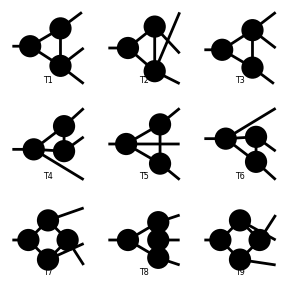

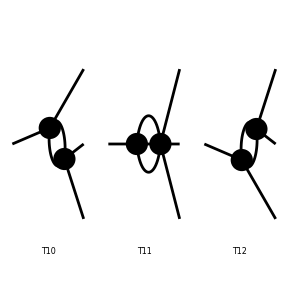

FeynArtsGraphics(1→3)(([T1] | [T2] | [T3]
[T4] | [T5] | [T6]
[T7] | [T8] | [T9]),([T10] | [T11] | [T12]
Null | Null | Null
Null | Null | Null))

```mathematica
Paint[tt]
```

```mathematica
diagrams = InsertFields[tt, {S[2]}-> {{S[1]}, {V[2]}, {V[1]}}, InsertionLevel-> {Particles}, Model->"THDM", Restrictions->{NoGeneration1, NoGeneration2, NoElectronHCoupling, NoLightFHCoupling}, ExcludeParticles->{V[5], F[1], F[2], -F[1], -F[2]}];
```

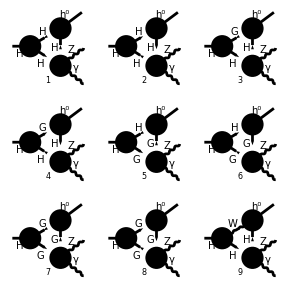

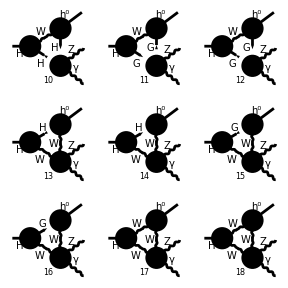

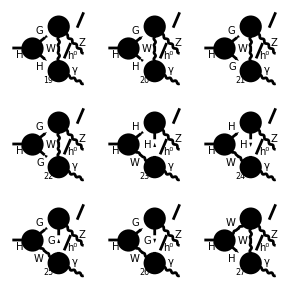

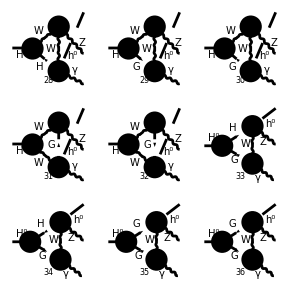

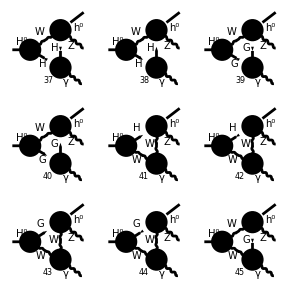

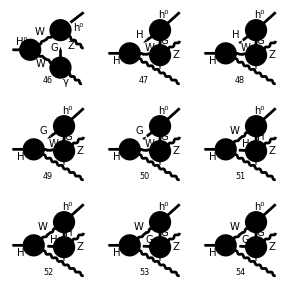

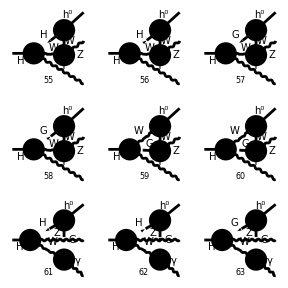

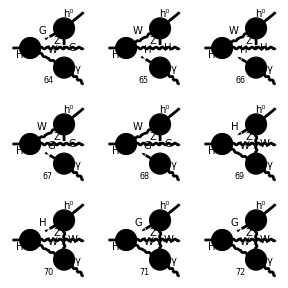

FeynArtsGraphics({ComposedChar(H,Null,0)}→{ComposedChar(h,Null,0),Z,\gamma})(([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9]),([10] | [11] | [12]
[13] | [14] | [15]
[16] | [17] | [18]),([19] | [20] | [21]
[22] | [23] | [24]
[25] | [26] | [27]),([28] | [29] | [30]
[31] | [32] | [33]
[34] | [35] | [36]),([37] | [38] | [39]
[40] | [41] | [42]
[43] | [44] | [45]),([46] | [47] | [48]
[49] | [50] | [51]
[52] | [53] | [54]),([55] | [56] | [57]
[58] | [59] | [60]
[61] | [62] | [63]),([64] | [65] | [66]
[67] | [68] | [69]
[70] | [71] | [72]),([73] | [74] | [75]
[76] | [77] | [78]
[79] | [80] | [81]),([82] | [83] | [84]
[85] | [86] | [87]
[88] | [89] | [90]),([91] | [92] | [93]
[94] | [95] | [96]
[97] | [98] | [99]),([100] | [101] | [102]
[103] | [104] | [105]
[106] | [107] | [108]),([109] | [110] | [111]
[112] | [113] | [114]
[115] | [116] | [117]),([118] | [119] | [120]
[121] | [122] | [123]
[124] | [125] | [126]),([127] | [128] | [129]
[130] | [131] | [132]
[133] | [134] | [135]),([136] | [137] | [138]
[139] | [140] | [141]
[142] | [143] | [144]),([145] | [146] | [147]
[148] | [149] | [150]
[151] | [152] | [153]),([154] | [155] | [156]
[157] | [158] | [159]
[160] | [161] | [162]),([163] | [164] | [165]
[166] | [167] | [168]
[169] | [170] | [171]),([172] | [173] | [174]
[175] | [176] | [177]
[178] | [179] | [180]),([181] | [182] | [183]
[184] | [185] | [186]
[187] | [188] | [189]),([190] | [191] | [192]
[193] | [194] | [195]
[196] | [197] | [198]),([199] | [200] | [201]
[202] | [203] | [204]
[205] | [206] | [207]),([208] | [209] | [210]
[211] | [212] | [213]
[214] | [215] | [216]),([217] | [218] | [219]
[220] | [221] | [222]
[223] | [224] | [225]),([226] | [227] | [228]
[229] | [230] | [231]
[232] | [233] | [234]),([235] | [236] | [237]
[238] | [239] | [240]
[241] | [242] | [243]),([244] | [245] | [246]
[247] | [248] | [249]
[250] | [251] | [252]),([253] | [254] | [255]
[256] | [257] | [258]
[259] | [260] | [261]),([262] | [263] | [264]
[265] | [266] | Null
Null | Null | Null))

```mathematica
Paint[diagrams, Numbering->Simple]
```

```mathematica
TriangleList = Range[80];
BoxesList = Range[81, 256];
TwoPoints = Range[257, 266];
```

```mathematica
trianglewithoutW = DiagramSelect[DiagramExtract[diagrams, TriangleList], FreeQ[LoopFields[##],  V[3]]&];
trianglewithH = DiagramSelect[DiagramExtract[diagrams, TriangleList],
!FreeQ[LoopFields[##], S[5]]&];
```

```mathematica
(* triangle charged H contribution and triangle charged W+/- and charged Goldstone G+/- *)
trianglewithoutH = DiagramSelect[DiagramExtract[diagrams, TriangleList], FreeQ[LoopFields[##],  S[5]]&];
triangleH = DiagramSelect[trianglewithoutW, FreeQ[LoopFields[##], S[6]]&];
triangleHGW = DiagramComplement[trianglewithH, triangleH];
```

```mathematica
Clear[trianglewithoutWG, trianglewithoutG, trianglewithoutG0]
```

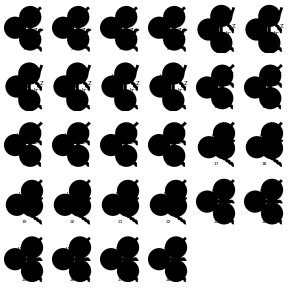

```mathematica
pTriangleHGW = Paint[triangleHGW, Numbering->Simple, ColumnsXRows->{6,5}, SheetHeader->None];
```

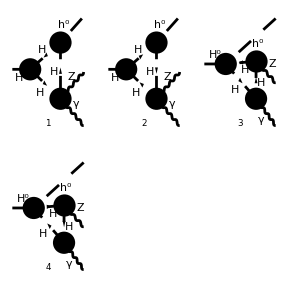

FeynArtsGraphics()(([1] | [2] | [3]
[4] | Null | Null
Null | Null | Null))

```mathematica
ptriangleH = Paint[triangleH, Numbering->Simple, SheetHeader->None]
```

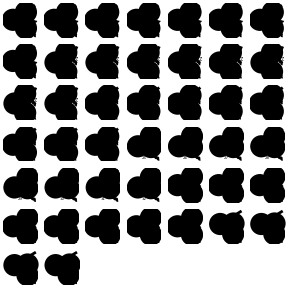

FeynArtsGraphics()(([1] | [2] | [3] | [4] | [5] | [6] | [7]
[8] | [9] | [10] | [11] | [12] | [13] | [14]
[15] | [16] | [17] | [18] | [19] | [20] | [21]
[22] | [23] | [24] | [25] | [26] | [27] | [28]
[29] | [30] | [31] | [32] | [33] | [34] | [35]
[36] | [37] | [38] | [39] | [40] | [41] | [42]
[43] | [44] | Null | Null | Null | Null | Null))

```mathematica
ptrianglewithoutH = Paint[trianglewithoutH, Numbering->Simple, SheetHeader->None, ColumnsXRows->{7,7}]
```

```mathematica
Export["triangleHGW.pdf", pTriangleHGW]
```

{triangleHGW.pdf}

```mathematica
Export["triangleH.pdf", ptriangleH]
```

{triangleH.pdf}

```mathematica
Export["trianglewithoutH.pdf", ptrianglewithoutH]
```

{trianglewithoutH.pdf}

```mathematica
Clear[BoxesWithoutFermion, BoxesRemain, BoxesHWGu, BoxesMixed]
```

```mathematica
BoxesDiagrams = DiagramExtract[diagrams, BoxesList];
BoxesWithH = DiagramSelect[BoxesDiagrams,
!FreeQ[LoopFields[##], S[5]]&];
BoxesWithFermion =  DiagramSelect[BoxesDiagrams,
!FreeQ[LoopFields[##], F[3, {3, _}]]&];
BoxesWithoutW =  DiagramSelect[BoxesDiagrams,
FreeQ[LoopFields[##], V[3]]&];
```

```mathematica
BoxesWithoutWG = DiagramSelect[BoxesWithoutW, FreeQ[LoopFields[##],  S[6]]&];
BoxesWithoutWGt = DiagramComplement[BoxesWithoutWG, BoxesWithFermion];
BoxesWithoutWGtu = DiagramSelect[BoxesWithoutWGt, FreeQ[LoopFields[##], U[_]]&];
```

```mathematica
BoxesH = BoxesWithoutWGtu;
BoxesWithoutH= DiagramComplement[BoxesDiagrams, BoxesWithH];
BoxesHGWu = DiagramComplement[BoxesWithH, BoxesH];
BoxesGWu = DiagramComplement[BoxesDiagrams,  BoxesWithH, BoxesWithFermion];
```

```mathematica
pBoxesH =Paint[BoxesH, Numbering->Simple, SheetHeader->None];
```

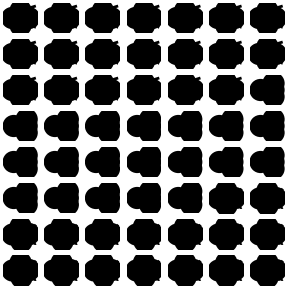

FeynArtsGraphics()(([1] | [2] | [3] | [4] | [5] | [6] | [7]
[8] | [9] | [10] | [11] | [12] | [13] | [14]
[15] | [16] | [17] | [18] | [19] | [20] | [21]
[22] | [23] | [24] | [25] | [26] | [27] | [28]
[29] | [30] | [31] | [32] | [33] | [34] | [35]
[36] | [37] | [38] | [39] | [40] | [41] | [42]
[43] | [44] | [45] | [46] | [47] | [48] | [49]
[50] | [51] | [52] | [53] | [54] | [55] | [56]
Null | Null | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null))

```mathematica
pBoxesHGWu = Paint[BoxesHGWu, Numbering->Simple, SheetHeader->None, ColumnsXRows->{7,10}]
```

```mathematica
pBoxesGWu = Paint[BoxesGWu, Numbering->Simple, SheetHeader->None, ColumnsXRows->{10, 11}]
```

-Graphics-

FeynArtsGraphics()(([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20]
[21] | [22] | [23] | [24] | [25] | [26] | [27] | [28] | [29] | [30]
[31] | [32] | [33] | [34] | [35] | [36] | [37] | [38] | [39] | [40]
[41] | [42] | [43] | [44] | [45] | [46] | [47] | [48] | [49] | [50]
[51] | [52] | [53] | [54] | [55] | [56] | [57] | [58] | [59] | [60]
[61] | [62] | [63] | [64] | [65] | [66] | [67] | [68] | [69] | [70]
[71] | [72] | [73] | [74] | [75] | [76] | [77] | [78] | [79] | [80]
[81] | [82] | [83] | [84] | [85] | [86] | [87] | [88] | [89] | [90]
[91] | [92] | [93] | [94] | [95] | [96] | [97] | [98] | [99] | [100]
[101] | [102] | [103] | [104] | [105] | [106] | [107] | [108] | Null | Null))

```mathematica
Export["BoxesH.pdf",  pBoxesH];
Export ["BoxesHGWu.pdf", pBoxesHGWu];
Export["BoxesGWu.pdf", pBoxesGWu];
```

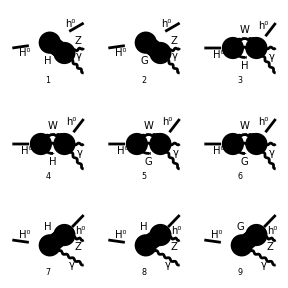

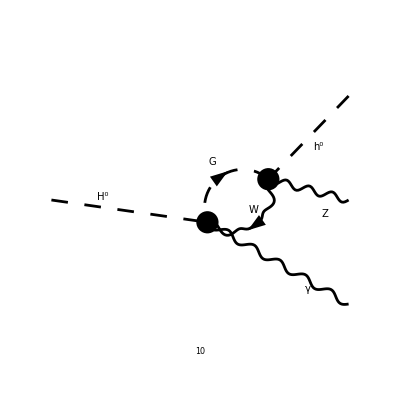

```mathematica
(*2 points*)
TwoPointsDiagrams = DiagramExtract[diagrams, TwoPoints];
Paint[TwoPointsDiagrams, Numbering->Simple];
```

```mathematica
PureH = DiagramExtract[TwoPointsDiagrams, {1}];
HGWu = DiagramExtract[TwoPointsDiagrams, {3,4,7,8}];
GWu = DiagramExtract[TwoPointsDiagrams, {2,5,6,9,10}];
```

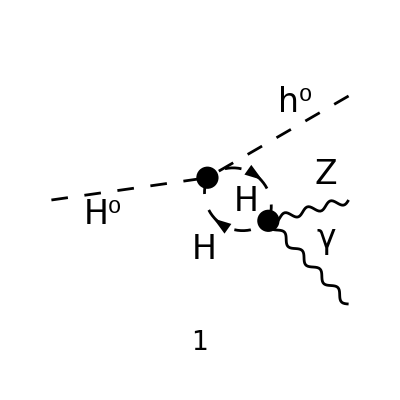

FeynArtsGraphics()(([1]))

```mathematica
pPureH = Paint[PureH, Numbering->Simple, SheetHeader->None,  ColumnsXRows->{1,1}]
```

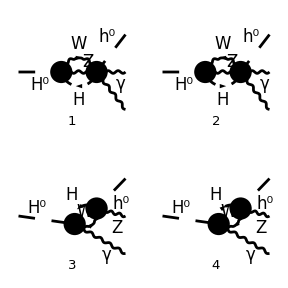

FeynArtsGraphics()(([1] | [2]
[3] | [4]))

```mathematica
pHGWu = Paint[HGWu, Numbering->Simple, SheetHeader->None, ColumnsXRows->{2,2}]
```

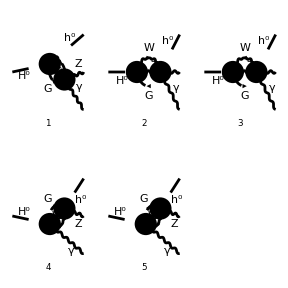

FeynArtsGraphics()(([1] | [2] | [3]
[4] | [5] | Null))

```mathematica
pGWu = Paint[GWu, Numbering->Simple, SheetHeader-> None, ColumnsXRows->{3,2}]
```

```mathematica
Export["pureH.pdf", pPureH];
Export["HGWu.pdf", pHGWu];
Export["GWu.pdf", pGWu];
```

```mathematica
Clear[amps]
```

```mathematica
Clear[amps];
ConventionNotation = {CAB-> Cos[α + β], CBA-> Cos[β-α], SAB-> Sin[α + β], SBA-> Sin[β-α], S2B-> Sin[2 β], C2B->Cos[2 β], S2A-> Sin[2 α], C2A->Cos[2 α], Mh0-> Subscript[m, h], MHH->Subscript[m, H], MHp->Subscript[m, Hp], Lambda5 -> Subscript[λ, 5]}
amps = CreateFeynAmp[PureH, Truncated->True, GaugeRules->{_FAGaugeXi->1}]
amps = FCFAConvert[amps, IncomingMomenta->{q}, OutgoingMomenta->{k1, k2, k3},
LoopMomenta-> {l},  ChangeDimension->D, UndoChiralSplittings->True, DropSumOver->True , TransversePolarizationVectors->{k1, k2}, List->True, 
SMP->True, LorentzIndexNames->{μ, ν, ρ, σ, δ, λ}, SUNIndexNames->{a,b,c,d,f,e,g,h},SUNFIndexNames-> {w,v,z,x,m,n,q,r}
]//Contract//FCTraceFactor//Simplify
```

{CAB→cos(α+β),CBA→cos(α-β),SAB→sin(α+β),SBA→-sin(α-β),S2B→sin(2 β),C2B→cos(2 β),S2A→sin(2 α),C2A→cos(2 α),Mh0→m_h,MHH→m_H,MHp→m_Hp,Lambda5→λ_5}

FAFeynAmpList(Process→(S(2) | p1 | MHH | {})→(S(1) | k1 | Mh0 | {}
V(2) | k2 | FCGV(MZ) | {}
V(1) | k3 | 0 | {}),Model→{THDM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{-F(1),F(1),-F(2),F(2),-F(1,{1}),F(1,{1}),-F(1,{2}),F(1,{2}),-F(1,{3}),F(1,{3}),-F(2,{1}),F(2,{1}),-F(2,{2}),F(2,{2}),-F(2,{3}),F(2,{3}),-F(3,{1,_}),F(3,{1,_}),-F(3,{2,_}),F(3,{2,_}),-F(4,{1,_}),F(4,{1,_}),-F(4,{2,_}),F(4,{2,_})},ExcludeFieldPoints→{FieldPoint(0)(-F(1),F(2),-S(5)),FieldPoint(0)(-F(1),F(2),-S(6)),FieldPoint(0)(F(1),-F(2),S(5)),FieldPoint(0)(F(1),-F(2),S(6)),FieldPoint(0)(-F(2),F(2),S(1)),FieldPoint(0)(-F(2),F(2),S(2)),FieldPoint(0)(-F(2),F(2),S(3)),FieldPoint(0)(-F(2),F(2),S(4)),FieldPoint(0)(-F(4),F(4),S(1)),FieldPoint(0)(-F(4),F(4),S(2)),FieldPoint(0)(-F(4),F(4),S(3)),FieldPoint(0)(-F(4),F(4),S(4))},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[q1],(ⅈ (FCGV(EL))^4 ((FCGV(CW))^2-(FCGV(SW))^2) g(Lor1,Lor2) FAFeynAmpDenominator(1/((q1)^2-MHp^2),1/((-k2-k3+q1)^2-MHp^2)) (-(4 C2B Lambda5 S2A (FCGV(MW))^2 (FCGV(SW))^2)/(FCGV(EL))^2+CBA Mh0^2 S2A (2 CAB-S2B SBA)+CBA S2B^2 SBA (2 MHp^2-(4 Lambda5 (FCGV(MW))^2 (FCGV(SW))^2)/(FCGV(EL))^2)-MHH^2 S2A SBA (2 SAB-CBA S2B)))/(64 π^4 S2B^2 FCGV(CW) (FCGV(MW))^2 (FCGV(SW))^3)))

{(ⅈ e^2 g^μν ((cos(θ_W))^2-(sin(θ_W))^2) (e^2 (2 CAB CBA Mh0^2 S2A+CBA S2B SBA (Mh0^2 (-S2A)+MHH^2 S2A+2 MHp^2 S2B)-2 MHH^2 S2A SAB SBA)-4 Lambda5 m_W^2 (sin(θ_W))^2 (C2B S2A+CBA S2B^2 SBA)))/(64 π^4 S2B^2 m_W^2 (cos(θ_W)) (sin(θ_W))^3 (l^2-MHp^2).((k2+k3-l)^2-MHp^2))}

```mathematica
amps/.ConventionNotation
```

{(ⅈ e^2 csc^2(2 β) g^μν ((cos(θ_W))^2-(sin(θ_W))^2) (e^2 (-sin(2 β) sin(α-β) cos(α-β) (-sin(2 α) m_h^2+sin(2 α) m_H^2+2 sin(2 β) m_Hp^2)+2 sin(2 α) m_h^2 cos(α-β) cos(α+β)+2 sin(2 α) m_H^2 sin(α-β) sin(α+β))-4 λ_5 m_W^2 (sin(θ_W))^2 (sin(2 α) cos(2 β)-sin^2(2 β) sin(α-β) cos(α-β))))/(64 π^4 m_W^2 (cos(θ_W)) (sin(θ_W))^3 (l^2-m_Hp^2).((k2+k3-l)^2-m_Hp^2))}

```mathematica
amps/.ConventionNotation
```

{(ⅈ e^2 csc^2(2 β) g^μν ((cos(θ_W))^2-(sin(θ_W))^2) (e^2 (-sin(2 β) sin(α-β) cos(α-β) (-sin(2 α) m_h^2+sin(2 α) m_H^2+2 sin(2 β) m_Hp^2)+2 sin(2 α) m_h^2 cos(α-β) cos(α+β)+2 sin(2 α) m_H^2 sin(α-β) sin(α+β))-4 λ_5 m_W^2 (sin(θ_W))^2 (sin(2 α) cos(2 β)-sin^2(2 β) sin(α-β) cos(α-β))))/(64 π^4 m_W^2 (cos(θ_W)) (sin(θ_W))^3 (l^2-m_Hp^2).((k2+k3-l)^2-m_Hp^2))}

```mathematica
Pair[Momentum[k1, D], Momentum[k1, D]] =  Subscript[m, Z]^2
Pair[Momentum[k2, D], Momentum[k2, D]] =  0
Pair[Momentum[k3, D], Momentum[k3, D]] =Subscript[m, h]^2
 Pair[Momentum[k2, D], Momentum[k3, D]] = (Subscript[s, 23] - Subscript[m, h]^2)/2
Pair[Momentum[k1, D], Momentum[k2, D]] = (Subscript[s, 12] - Subscript[m, Z]^2)/2 
Pair[Momentum[k1, D], Momentum[k3, D]] = (Subscript[s, 13]  - Subscript[m, Z]^2 - Subscript[m, h]^2)/2
```

m_Z^2

0

m_h^2

1/2 (s_23-m_h^2)

1/2 (s_12-m_Z^2)

1/2 (-m_h^2-m_Z^2+s_13)

```mathematica
amps2 =(amps/.ConventionNotation // DiracSimplify)[[1]] // TID[#, l, ToPaVe->True]&
```

-((e^2 g^μν ((cos(θ_W))^2-(sin(θ_W))^2) B_0(s_23,m_Hp^2,m_Hp^2) (2 e^2 sin(2 α) csc^2(2 β) m_h^2 cos(α-β) cos(α+β)+e^2 sin(2 α) csc(2 β) m_h^2 sin(α-β) cos(α-β)+2 e^2 sin(2 α) csc^2(2 β) m_H^2 sin(α-β) sin(α+β)-e^2 sin(2 α) csc(2 β) m_H^2 sin(α-β) cos(α-β)-2 e^2 m_Hp^2 sin(α-β) cos(α-β)+4 λ_5 m_W^2 sin(α-β) cos(α-β) (sin(θ_W))^2-4 λ_5 sin(2 α) cot(2 β) csc(2 β) m_W^2 (sin(θ_W))^2))/(64 π^2 m_W^2 (cos(θ_W)) (sin(θ_W))^3))

```mathematica
PaXEvaluate[ B0[Pair[Momentum[k2,D],Momentum[k2,D]]+2 Pair[Momentum[k2,D],Momentum[k3,D]]+Pair[Momentum[k3,D],Momentum[k3,D]],Subscript[m, Hp]^2,Subscript[m, Hp]^2]]
```

1/ε-(-s_23 log(μ^2/(π m_Hp^2))-√(s_23 (s_23-4 m_Hp^2)) log((√(s_23 (s_23-4 m_Hp^2))+2 m_Hp^2-s_23)/(2 m_Hp^2))+ℽ s_23-2 s_23)/s_23

```mathematica
PaXEvaluateUV[amps2]
```

-((e^2 g^μν (cos(θ_W)-sin(θ_W)) (cos(θ_W)+sin(θ_W)) (3 e^2 sin(2 α) cos(2 α) csc^2(2 β) m_h^2+e^2 sin(2 α) csc^2(2 β) m_h^2 cos(2 (α-2 β))+4 e^2 sin(2 α) cot(2 β) csc(2 β) m_h^2-3 e^2 sin(2 α) cos(2 α) csc^2(2 β) m_H^2-e^2 sin(2 α) csc^2(2 β) m_H^2 cos(2 (α-2 β))+4 e^2 sin(2 α) cot(2 β) csc(2 β) m_H^2-4 e^2 m_Hp^2 sin(2 (α-β))+8 λ_5 m_W^2 sin(2 (α-β)) (sin(θ_W))^2-16 λ_5 sin(2 α) cot(2 β) csc(2 β) m_W^2 (sin(θ_W))^2))/(256 π^2 m_W^2 ε_UV (cos(θ_W)) (sin(θ_W))^3))

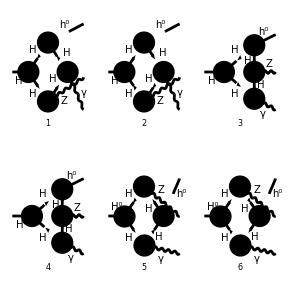

FeynArtsGraphics({ComposedChar(H,Null,0)}→{ComposedChar(h,Null,0),Z,\gamma})(([1] | [2] | [3]
[4] | [5] | [6]
Null | Null | Null))

```mathematica
Paint[BoxesH, Numbering->Simple]
```

```mathematica
Clear[ampsBoxes]
ampsBoxes = CreateFeynAmp[BoxesH, Truncated->True, GaugeRules->{_FAGaugeXi->1}];
ampsBoxes = FCFAConvert[ampsBoxes, IncomingMomenta->{q}, OutgoingMomenta->{k1, k2, k3},
LoopMomenta-> {l},  ChangeDimension->D, UndoChiralSplittings->True, DropSumOver->True , TransversePolarizationVectors->{k1, k2}, List->True, 
SMP->True, LorentzIndexNames->{μ, ν, ρ, σ, δ, λ}, SUNIndexNames->{a,b,c,d,f,e,g,h},SUNFIndexNames-> {w,v,z,x,m,n,q,r}
]//Contract//FCTraceFactor//Simplify;
```

```mathematica
(* Projections*)
P1[μ,ν] := (Subscript[m, Z]^2 - Subscript[s, 12]) MTD[μ,ν]/2 - Pair[Momentum[k1, D], LorentzIndex[μ, D]] Pair[ Momentum[k2, D], LorentzIndex[ν, D]]
P2[μ,ν] := Pair[Momentum[k1, D], LorentzIndex[μ,D]]  Pair[Momentum[k3, D], LorentzIndex[ν,D]] +  (Subscript[m, Z]^2 - Subscript[s, 12])(Pair[Momentum[k3, D], LorentzIndex[μ,D]]  Pair[Momentum[k3, D], LorentzIndex[ν,D]])/(2 Subscript[m, h]^2)
P3[μ,ν] := Pair[Momentum[k2, D], LorentzIndex[ν,D]]  Pair[Momentum[k3, D], LorentzIndex[μ,D]] +  (Subscript[m, Z]^2 - Subscript[s, 23])(Pair[Momentum[k3, D], LorentzIndex[μ,D]]  Pair[Momentum[k3, D], LorentzIndex[ν,D]])/(2 Subscript[m, h]^2)
```

```mathematica
P1[μ,ν]
P2[μ,ν]
P3[μ,ν]
```

1/2 g^μν (m_Z^2-s_12)-k1^μ k2^ν

(k3^μ k3^ν (m_Z^2-s_12))/(2 m_h^2)+k1^μ k3^ν

(k3^μ k3^ν (m_Z^2-s_23))/(2 m_h^2)+k2^ν k3^μ

```mathematica
ampsBoxes1 = ChangeDimension[ampsBoxes[[1]]/.ConventionNotation//DiracSimplify, D]
```

-((ⅈ csc^2(2 β) ((cos(θ_W))^2-(sin(θ_W))^2) (2 k1+k3-2 l)^ν (2 k1+k2+2 k3-2 l)^μ (e^2 (-sin(2 β) sin(α-β) (m_h^2-2 m_Hp^2)-2 m_h^2 cos(α+β))+4 λ_5 m_W^2 cos(α+β) (sin(θ_W))^2) (e^2 (sin(2 β) cos(α-β) (m_H^2-2 m_Hp^2)-2 m_H^2 sin(α+β))+4 λ_5 m_W^2 sin(α+β) (sin(θ_W))^2))/(128 π^4 m_W^2 (cos(θ_W)) (sin(θ_W))^3 (l^2-m_Hp^2).((k1-l)^2-m_Hp^2).((k1+k3-l)^2-m_Hp^2).((k1+k2+k3-l)^2-m_Hp^2)))

```mathematica
A3 = P1[μ,ν] ampsBoxes1 // Contract
A4 = P2[μ,ν] ampsBoxes1 // Contract
A8 = P3[μ,ν] ampsBoxes1 // Contract
```

-((ⅈ csc^2(2 β) ((cos(θ_W))^2-(sin(θ_W))^2) (2 m_h^2 (k1·l)+4 m_h^2 (k2·l)-4 s_12 m_h^2-s_13 m_h^2-s_23 m_h^2+3 m_h^2 m_Z^2+m_h^4+8 (k1·l) (k2·l)+12 m_Z^2 (k1·l)-12 s_12 (k1·l)-2 s_23 (k1·l)-4 s_12 (k2·l)-4 s_13 (k2·l)+6 m_Z^2 (k3·l)-6 s_12 (k3·l)-4 l^2 m_Z^2+4 l^2 s_12-s_12 m_Z^2-5 s_13 m_Z^2-m_Z^4+2 s_12^2+5 s_12 s_13+s_12 s_23+s_13 s_23) (e^2 sin(2 β) m_h^2 sin(α-β)+2 e^2 m_h^2 cos(α+β)-2 e^2 sin(2 β) m_Hp^2 sin(α-β)-4 λ_5 m_W^2 cos(α+β) (sin(θ_W))^2) (-2 e^2 m_H^2 sin(α+β)+e^2 sin(2 β) m_H^2 cos(α-β)-2 e^2 sin(2 β) m_Hp^2 cos(α-β)+4 λ_5 m_W^2 sin(α+β) (sin(θ_W))^2))/(256 π^4 m_W^2 (cos(θ_W)) (sin(θ_W))^3 (l^2-m_Hp^2).((k1-l)^2-m_Hp^2).((k1+k3-l)^2-m_Hp^2).((k1+k2+k3-l)^2-m_Hp^2)))

(ⅈ csc^2(2 β) ((cos(θ_W))^2-(sin(θ_W))^2) (2 (k3·l)+m_Z^2-s_13) (8 m_h^2 (k1·l)-s_12 m_h^2-4 s_13 m_h^2-3 m_h^2 m_Z^2+4 m_h^4+4 m_Z^2 (k3·l)-4 s_12 (k3·l)-2 s_12 m_Z^2-2 s_13 m_Z^2-s_23 m_Z^2+2 m_Z^4+2 s_12 s_13+s_12 s_23) (e^2 sin(2 β) m_h^2 sin(α-β)+2 e^2 m_h^2 cos(α+β)-2 e^2 sin(2 β) m_Hp^2 sin(α-β)-4 λ_5 m_W^2 cos(α+β) (sin(θ_W))^2) (-2 e^2 m_H^2 sin(α+β)+e^2 sin(2 β) m_H^2 cos(α-β)-2 e^2 sin(2 β) m_Hp^2 cos(α-β)+4 λ_5 m_W^2 sin(α+β) (sin(θ_W))^2))/(512 π^4 m_h^2 m_W^2 (cos(θ_W)) (sin(θ_W))^3 (l^2-m_Hp^2).((k1-l)^2-m_Hp^2).((k1+k3-l)^2-m_Hp^2).((k1+k2+k3-l)^2-m_Hp^2))

(ⅈ csc^2(2 β) ((cos(θ_W))^2-(sin(θ_W))^2) (-m_h^2+4 (k3·l)+2 m_Z^2-2 s_13-s_23) (4 m_h^2 (k2·l)-2 s_12 m_h^2-s_23 m_h^2+2 m_h^2 m_Z^2+m_h^4+2 m_Z^2 (k3·l)-2 s_23 (k3·l)-s_13 m_Z^2-s_23 m_Z^2+m_Z^4+s_13 s_23) (e^2 sin(2 β) m_h^2 sin(α-β)+2 e^2 m_h^2 cos(α+β)-2 e^2 sin(2 β) m_Hp^2 sin(α-β)-4 λ_5 m_W^2 cos(α+β) (sin(θ_W))^2) (-2 e^2 m_H^2 sin(α+β)+e^2 sin(2 β) m_H^2 cos(α-β)-2 e^2 sin(2 β) m_Hp^2 cos(α-β)+4 λ_5 m_W^2 sin(α+β) (sin(θ_W))^2))/(512 π^4 m_h^2 m_W^2 (cos(θ_W)) (sin(θ_W))^3 (l^2-m_Hp^2).((k1-l)^2-m_Hp^2).((k1+k3-l)^2-m_Hp^2).((k1+k2+k3-l)^2-m_Hp^2))

```mathematica
paveD = A3// ToPaVe[#, l]&//Simplify
```

(((cos(θ_W))^2-(sin(θ_W))^2) (e^2 ((2 cos(α+β) csc(2 β)+sin(α-β)) m_h^2-2 sin(α-β) m_Hp^2)-4 cos(α+β) csc(2 β) m_W^2 (sin(θ_W))^2 λ_5) ((8 ⅈ (k1·l) (k2·l) (e^2 (2 cos(α-β) m_Hp^2-(cos(α-β)-2 csc(2 β) sin(α+β)) m_H^2)-4 csc(2 β) sin(α+β) m_W^2 (sin(θ_W))^2 λ_5))/(l^2-m_Hp^2).((k1-l)^2-m_Hp^2).((k1+k3-l)^2-m_Hp^2).((k1+k2+k3-l)^2-m_Hp^2)+(6 ⅈ (k3·l) (m_Z^2-s_12) (e^2 (2 cos(α-β) m_Hp^2-(cos(α-β)-2 csc(2 β) sin(α+β)) m_H^2)-4 csc(2 β) sin(α+β) m_W^2 (sin(θ_W))^2 λ_5))/(l^2-m_Hp^2).((k1-l)^2-m_Hp^2).((k1+k3-l)^2-m_Hp^2).((k1+k2+k3-l)^2-m_Hp^2)+(4 ⅈ (k2·l) (m_h^2-s_12-s_13) (e^2 (2 cos(α-β) m_Hp^2-(cos(α-β)-2 csc(2 β) sin(α+β)) m_H^2)-4 csc(2 β) sin(α+β) m_W^2 (sin(θ_W))^2 λ_5))/(l^2-m_Hp^2).((k1-l)^2-m_Hp^2).((k1+k3-l)^2-m_Hp^2).((k1+k2+k3-l)^2-m_Hp^2)+(2 ⅈ (k1·l) (m_h^2+6 m_Z^2-6 s_12-s_23) (e^2 (2 cos(α-β) m_Hp^2-(cos(α-β)-2 csc(2 β) sin(α+β)) m_H^2)-4 csc(2 β) sin(α+β) m_W^2 (sin(θ_W))^2 λ_5))/(l^2-m_Hp^2).((k1-l)^2-m_Hp^2).((k1+k3-l)^2-m_Hp^2).((k1+k2+k3-l)^2-m_Hp^2)+(4 ⅈ l^2 (m_Z^2-s_12) (((cos(α-β)-2 csc(2 β) sin(α+β)) m_H^2-2 cos(α-β) m_Hp^2) e^2+4 csc(2 β) sin(α+β) m_W^2 (sin(θ_W))^2 λ_5))/(l^2-m_Hp^2).((k1-l)^2-m_Hp^2).((k1+k3-l)^2-m_Hp^2).((k1+k2+k3-l)^2-m_Hp^2)+π^2 D_0(0,m_h^2,m_Z^2,-m_h^2-m_Z^2+s_12+s_13+s_23,s_23,s_13,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2) (m_h^4+(3 m_Z^2-4 s_12-s_13-s_23) m_h^2-m_Z^4+2 s_12^2+5 s_12 s_13-m_Z^2 (s_12+5 s_13)+s_12 s_23+s_13 s_23) (((cos(α-β)-2 csc(2 β) sin(α+β)) m_H^2-2 cos(α-β) m_Hp^2) e^2+4 csc(2 β) sin(α+β) m_W^2 (sin(θ_W))^2 λ_5)))/(256 π^4 (cos(θ_W)) m_W^2 (sin(θ_W))^3)

```mathematica
paveD//StandardForm
```

((SMP[cos_W]^2-SMP[sin_W]^2) (SMP[e]^2 ((2 Cos[α+β] Csc[2 β]+Sin[α-β]) m_h^2-2 Sin[α-β] m_Hp^2)-4 Cos[α+β] Csc[2 β] SMP[m_W]^2 SMP[sin_W]^2 λ_5) (8 ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[l,D],m_Hp],PropagatorDenominator[-Momentum[k1-l,D],m_Hp],PropagatorDenominator[-Momentum[k1+k3-l,D],m_Hp],PropagatorDenominator[-Momentum[k1+k2+k3-l,D],m_Hp]] Pair[Momentum[k1,D],Momentum[l,D]] Pair[Momentum[k2,D],Momentum[l,D]] (SMP[e]^2 (-((Cos[α-β]-2 Csc[2 β] Sin[α+β]) m_H^2)+2 Cos[α-β] m_Hp^2)-4 Csc[2 β] Sin[α+β] SMP[m_W]^2 SMP[sin_W]^2 λ_5)+6 ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[l,D],m_Hp],PropagatorDenominator[-Momentum[k1-l,D],m_Hp],PropagatorDenominator[-Momentum[k1+k3-l,D],m_Hp],PropagatorDenominator[-Momentum[k1+k2+k3-l,D],m_Hp]] Pair[Momentum[k3,D],Momentum[l,D]] (m_Z^2-s_12) (SMP[e]^2 (-((Cos[α-β]-2 Csc[2 β] Sin[α+β]) m_H^2)+2 Cos[α-β] m_Hp^2)-4 Csc[2 β] Sin[α+β] SMP[m_W]^2 SMP[sin_W]^2 λ_5)+4 ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[l,D],m_Hp],PropagatorDenominator[-Momentum[k1-l,D],m_Hp],PropagatorDenominator[-Momentum[k1+k3-l,D],m_Hp],PropagatorDenominator[-Momentum[k1+k2+k3-l,D],m_Hp]] Pair[Momentum[k2,D],Momentum[l,D]] (m_h^2-s_12-s_13) (SMP[e]^2 (-((Cos[α-β]-2 Csc[2 β] Sin[α+β]) m_H^2)+2 Cos[α-β] m_Hp^2)-4 Csc[2 β] Sin[α+β] SMP[m_W]^2 SMP[sin_W]^2 λ_5)+2 ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[l,D],m_Hp],PropagatorDenominator[-Momentum[k1-l,D],m_Hp],PropagatorDenominator[-Momentum[k1+k3-l,D],m_Hp],PropagatorDenominator[-Momentum[k1+k2+k3-l,D],m_Hp]] Pair[Momentum[k1,D],Momentum[l,D]] (m_h^2+6 m_Z^2-6 s_12-s_23) (SMP[e]^2 (-((Cos[α-β]-2 Csc[2 β] Sin[α+β]) m_H^2)+2 Cos[α-β] m_Hp^2)-4 Csc[2 β] Sin[α+β] SMP[m_W]^2 SMP[sin_W]^2 λ_5)+4 ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[l,D],m_Hp],PropagatorDenominator[-Momentum[k1-l,D],m_Hp],PropagatorDenominator[-Momentum[k1+k3-l,D],m_Hp],PropagatorDenominator[-Momentum[k1+k2+k3-l,D],m_Hp]] Pair[Momentum[l,D],Momentum[l,D]] (m_Z^2-s_12) (SMP[e]^2 ((Cos[α-β]-2 Csc[2 β] Sin[α+β]) m_H^2-2 Cos[α-β] m_Hp^2)+4 Csc[2 β] Sin[α+β] SMP[m_W]^2 SMP[sin_W]^2 λ_5)+π^2 D0[0,m_h^2,m_Z^2,-m_h^2-m_Z^2+s_12+s_13+s_23,s_23,s_13,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2] (m_h^4-m_Z^4+2 s_12^2+5 s_12 s_13-m_Z^2 (s_12+5 s_13)+m_h^2 (3 m_Z^2-4 s_12-s_13-s_23)+s_12 s_23+s_13 s_23) (SMP[e]^2 ((Cos[α-β]-2 Csc[2 β] Sin[α+β]) m_H^2-2 Cos[α-β] m_Hp^2)+4 Csc[2 β] Sin[α+β] SMP[m_W]^2 SMP[sin_W]^2 λ_5)))/(256 π^4 SMP[cos_W] SMP[m_W]^2 SMP[sin_W]^3)

```mathematica
d0 =π^2 D0[0,Subscript[m, h]^2,Subscript[m, Z]^2,-Subscript[m, h]^2-Subscript[m, Z]^2+Subscript[s, 12]+Subscript[s, 13]+Subscript[s, 23],Subscript[s, 23],Subscript[s, 13],Subscript[m, Hp]^2,Subscript[m, Hp]^2,Subscript[m, Hp]^2,Subscript[m, Hp]^2]
```

π^2 D_0(0,m_h^2,m_Z^2,-m_h^2-m_Z^2+s_12+s_13+s_23,s_23,s_13,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2)

```mathematica
d0//StandardForm
```

π^2 D0[0,m_h^2,m_Z^2,2 Pair[Momentum[k1,D],Momentum[k3,D]]+s_12+s_23,s_23,2 Pair[Momentum[k1,D],Momentum[k3,D]]+m_h^2+m_Z^2,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2]

```mathematica
resExpand = PaXEvaluate[d0, PaXD0Expand->True]
```

π^2 (1/(√(((2 m_Hp^2-m_h^2) (m_h^2+8)-1)^2-4 (1-1) (1/2 (2 m_Hp^2-m_Z^2+√(m_Z^2 1)) (s_23-m_h^2)-1)))-(1+13)/(√((1-1)^2-4 (1) (1))))
 |  |  |  |

```mathematica
PaXEvaluateIR[resExpand]
```

0

```mathematica
$ExcludeTopologies[Triangles1] = FreeQ[ToTree[#], Centre[4]]&;
$ExcludeTopologies[Triangles2] = FreeQ[ToTree[#], Centre[3]]&;
```

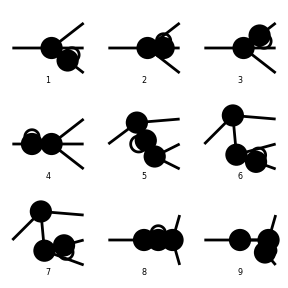

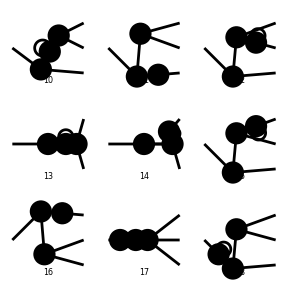

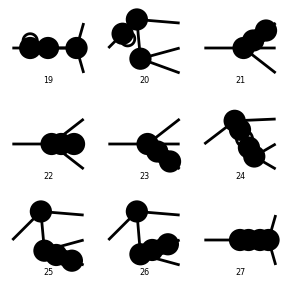

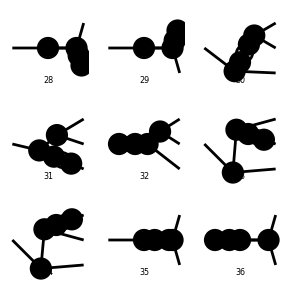

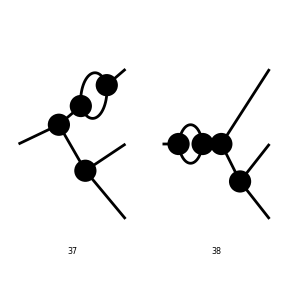

FeynArtsGraphics(1→3)(([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9]),([10] | [11] | [12]
[13] | [14] | [15]
[16] | [17] | [18]),([19] | [20] | [21]
[22] | [23] | [24]
[25] | [26] | [27]),([28] | [29] | [30]
[31] | [32] | [33]
[34] | [35] | [36]),([37] | [38] | Null
Null | Null | Null
Null | Null | Null))

```mathematica
tt2 = CreateTopologies[1, 1->3,  ExcludeTopologies->{Triangles1, Triangles2, Tadpoles}];
Paint[tt2, Numbering->Simple]
```